# A classical counterpart of the Unruh effect in relativistic fluids

## The following code generates the numerical figures used in the paper.

## Causal heat transient

```mathematica
κ=0.8;Subscript[c, v]=1;Subscript[τ, q]=1;w=1;   (* conductivity, heat capacity, relaxation time, enthalpy *)
A=0.6;σ=1.5;Subscript[x, 0]=2;   (* pulse height, width, probe worldline *)
L=40;tmax=12;xmax=12;   (* box, run time, plotted window *)
```

```mathematica
Subscript[v, c]=√(κ/(Subscript[c, v] Subscript[τ, q]))   (* second sound, Eq. (A4); has to stay below 1 *)
```

0.894427

```mathematica
Clear[δT,q];   (* the names have to be free before they are solved for *)
(* energy balance and the Maxwell–Cattaneo law, Eq. (A7a) *)
{δT,q}=NDSolveValue[{Subscript[c, v] D[δT[t,x], t]==-D[q[t,x], x],Subscript[τ, q] D[q[t,x], t]+q[t,x]==-κ D[δT[t,x], x],δT[0,x]==A ⅇ^(-x^2/(2 σ^2)),q[0,x]==0,δT[t,-L]==δT[t,L],q[t,-L]==q[t,L]},{δT,q},{t,0,tmax},{x,-L,L},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1600,"MaxPoints"->1600,"DifferenceOrder"->4}}];
```

## Shared styling

```mathematica
blue=RGBColor[0,0.447,0.698];verm=RGBColor[0.835,0.369,0.];red=RGBColor[0.8,0.1,0.1];   (* colour-blind safe *)
lab[e_]:=Style[e,FontFamily->"Times",FontSize->11,Black];it[s_]:=Style[s,Italic];
hue=Blend[{{-1,blue},{-0.5,Blend[{blue,White},0.45]},{0,GrayLevel[0.97]},{0.5,Blend[{verm,White},0.45]},{1,verm}},#]&;   (* diverging, neutral at q = 0 *)
```

## Figure 1 — space–time heat map

```mathematica
Subscript[q, max]=Ceiling[NMaxValue[{Abs[q[t,x]]/w,0≤t≤tmax&&-xmax≤x≤xmax},{t,x}],0.01];   (* symmetric colour scale *)
grid=Table[q[t,x]/w,{t,Subdivide[0,tmax,699]},{x,Subdivide[-xmax,xmax,699]}];
pix=Map[List@@hue[Clip[#/Subscript[q, max],{-1,1}]]&,grid,{2}];   (* a raster keeps the file small; the frame stays vector *)
```

```mathematica
Legended[Graphics[{Raster[pix,{{-xmax,0},{xmax,tmax}}],Directive[Black,AbsoluteThickness[1.2],Dashing[{0.022,0.015}]],Line[{{Subscript[x, 0],0},{Subscript[x, 0],tmax}}],Inset[Style[Row[{it["x"]," = ",2}],FontFamily->"Times",FontSize->9.5],{Subscript[x, 0]+0.7,0.955 tmax},{Left,Top},Background->Directive[White,Opacity[0.8]]]},Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[0.9]],FrameLabel->{lab[Row[{it["x"],"   [",it["c"]," ",Subscript[it["τ"], "q"],"]"}]],lab[Row[{"proper time   ",it["τ"],"   [",Subscript[it["τ"], "q"],"]"}]]},FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->10],PlotRange->{{-xmax,xmax},{0,tmax}},PlotRangePadding->None,AspectRatio->1.02,ImageSize->340,ImagePadding->{{52,8},{42,8}}],BarLegend[{hue[#/Subscript[q, max]]&,{-Subscript[q, max],Subscript[q, max]}},LegendLabel->Placed[lab[Row[{it["q"]," / (",it["ε"],"+",it["p"],")"}]],Right],LabelStyle->Directive[FontFamily->"Times",FontSize->10,Black],LegendMarkerSize->200]]
```

-Graphics-

## Figure 2 — rapidity and thermodynamic acceleration

```mathematica
f[t_?NumericQ]:=q[t,Subscript[x, 0]]/w;   (* boost velocity seen on the probe worldline *)
f1[t_?NumericQ]:=(Derivative[1,0][q][t,Subscript[x, 0]])/w;
f2[t_?NumericQ]:=(Derivative[2,0][q][t,Subscript[x, 0]])/w;   (* taken from the interpolation, not finite-differenced *)
```

```mathematica
η[t_?NumericQ]:=1/2 ArcTanh[2 f[t]];   (* Eq. (21) *)
Subscript[a, th][t_?NumericQ]:=f1[t]/(1-4 f[t]^2);   (* Eq. (22) *)
Subscript[a, th]'[t_?NumericQ]:=f2[t]/(1-4 f[t]^2)+(8 f[t] f1[t]^2)/((1-4 f[t]^2)^2);
R[t_?NumericQ]:=Abs[Subscript[a, th]'[t]]/(Subscript[a, th][t])^2;   (* Eq. (23) *)
```

```mathematica
tab=Table[{t,R[t]},{t,0.3,tmax-0.3,0.005}];
Subscript[t, min]=MinimalBy[tab,Last]⟦1,1⟧;
runs=Split[Select[tab,Last[#]<1&],#2⟦1⟧-#1⟦1⟧<0.02&];   (* contiguous stretches only *)
win=SelectFirst[runs,#⟦1,1⟧≤Subscript[t, min]≤#⟦-1,1⟧&];
{t1,t2}={win⟦1,1⟧,win⟦-1,1⟧};
Mean[Subscript[a, th]/@Subdivide[t1,t2,50]]   (* the value quoted in the caption *)
```

-0.031998

```mathematica
(* legend text *)
ηLab=Row[{it["η"],"(",it["τ"],") = ",Style["1/2",Small]," artanh[2",it["q"],"/(",it["ε"],"+",it["p"],")]"}];
aLab=Row[{Subscript[it["a"], "th"],"(",it["τ"],") = ",it["u"],"·∇",it["η"],"   [",Superscript[Subscript[it["τ"], "q"],"-1"],"]"}];
τLab=Row[{it["τ"],"   [",Subscript[it["τ"], "q"],"]"}];
```

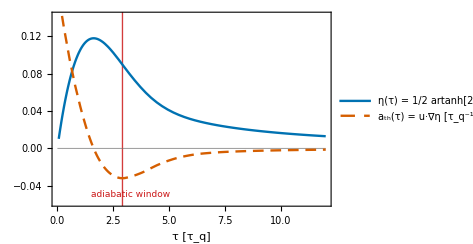

```mathematica
Plot[{η[t],Subscript[a, th][t]},{t,0.06,tmax},PlotStyle->{Directive[blue,AbsoluteThickness[1.7]],Directive[verm,AbsoluteThickness[1.7],Dashing[{0.022,0.014}]]},PlotRange->{{0,tmax},{-0.058,0.142}},Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[0.9]],FrameLabel->{lab[τLab],None},FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->10],Prolog->{Directive[red,Opacity[0.85],AbsoluteThickness[1.4]],Rectangle[{t1,-1},{t2,1}],Directive[GrayLevel[0.45],AbsoluteThickness[0.6]],Line[{{0,0},{tmax,0}}]},Epilog->{Text[Style["adiabatic window",FontFamily->"Times",FontSize->9,red],{t2+0.35,-0.0495},{-1,0}]},PlotLegends->Placed[LineLegend[{Directive[blue,AbsoluteThickness[1.7]],Directive[verm,AbsoluteThickness[1.7],Dashing[{0.022,0.014}]]},{lab[ηLab],lab[aLab]},LegendMarkerSize->26,Spacings->0.35],{0.63,0.86}],ImageSize->350,AspectRatio->0.7,ImagePadding->{{46,10},{42,8}}]
```

## Figure 3 — the exact transient response

```mathematica
(* the response needs second derivatives of the heat field; the grid solution above cannot supply them, so the same linear pair is solved exactly in Fourier space *)
(* q now names the grid solution, so the relaxation time is read back off Eq. (A4) *)
Subscript[τ, rel]=κ/(Subscript[c, v] Subscript[v, c]^2);
Subscript[T, 0][k_]:=A σ √(2 π) ⅇ^(1/2 (-σ^2) k^2);
(* the two telegrapher roots *)
Subscript[λ, pm][k_]:=1/2 (-1/Subscript[τ, rel]+{1,-1} √(1/Subscript[τ, rel]^2-4 Subscript[v, c]^2 k^2));
G[m_,t_,k_]:=Module[{l=Subscript[λ, pm][k]},(l⟦2⟧^m ⅇ^(l⟦2⟧ t)-l⟦1⟧^m ⅇ^(l⟦1⟧ t))/(l⟦1⟧-l⟦2⟧)];
```

```mathematica
(* mixed derivative of order m in t and n in x, to machine precision *)
Q[m_,n_][t_?NumericQ,x_?NumericQ]:=1/(2 π)NIntegrate[Re[((ⅈ k)^n ⅇ^(ⅈ k x) ⅈ κ Subscript[T, 0][k] k G[m,t,k])/Subscript[τ, rel]],{k,-7,0,7},Method->{"GaussKronrodRule","Points"->21},AccuracyGoal->13,PrecisionGoal->13,MaxRecursion->14];
```

```mathematica
g[t_,x_]:=1-4 (Q[0,0][t,x])^2;   (* from Eq. (14) *)
ηf[t_?NumericQ,x_?NumericQ]:=1/2 ArcTanh[2 Q[0,0][t,x]];
ηt[t_?NumericQ,x_?NumericQ]:=(Q[1,0][t,x])/g[t,x];
ηx[t_?NumericQ,x_?NumericQ]:=(Q[0,1][t,x])/g[t,x];
ηtt[t_?NumericQ,x_?NumericQ]:=(Q[2,0][t,x])/g[t,x]+(8 Q[0,0][t,x] (Q[1,0][t,x])^2)/g[t,x]^2;
ηtx[t_?NumericQ,x_?NumericQ]:=(Q[1,1][t,x])/g[t,x]+(8 Q[0,0][t,x] Q[1,0][t,x] Q[0,1][t,x])/g[t,x]^2;
ηxx[t_?NumericQ,x_?NumericQ]:=(Q[0,2][t,x])/g[t,x]+(8 Q[0,0][t,x] (Q[0,1][t,x])^2)/g[t,x]^2;
```

```mathematica
(* the energy-frame worldline in its own proper time, and the retarded null coordinate along it *)
(* a little past the plotted range, so the point splitting below never runs off the end *)
Subscript[τ, max]=11.7;
{tW,xW,UW}=NDSolveValue[{tw'[s]==Cosh[ηf[tw[s],xw[s]]],xw'[s]==Sinh[ηf[tw[s],xw[s]]],Uw'[s]==ⅇ^(-ηf[tw[s],xw[s]]),tw[0]==0,xw[0]==Subscript[x, 0],Uw[0]==0},{tw,xw,Uw},{s,0,Subscript[τ, max]},AccuracyGoal->11,PrecisionGoal->11];
```

```mathematica
χ[s_?NumericQ]:=ηf[tW[s],xW[s]];
Subscript[α, L][s_?NumericQ]:=Cosh[χ[s]] ηt[tW[s],xW[s]]+Sinh[χ[s]] ηx[tW[s],xW[s]];   (* Eq. (18) *)
Subscript[α, L]'[s_?NumericQ]:=Module[{c=Cosh[χ[s]],h=Sinh[χ[s]],T=tW[s],X=xW[s],a=Subscript[α, L][s]},a (h ηt[T,X]+c ηx[T,X])+c (c ηtt[T,X]+h ηtx[T,X])+h (c ηtx[T,X]+h ηxx[T,X])];
Subscript[R, U][s_?NumericQ]:=(Subscript[α, L][s])^2+2 Subscript[α, L]'[s];   (* 24 π Subscript[τ, rel]^2 Subscript[P, U]/𝒩, Eq. (40) *)
Subscript[R, sym][s_?NumericQ]:=2 (Subscript[α, L][s])^2;
```

```mathematica
(* the same excess taken straight from the correlator; the two splittings are Richardson extrapolated, and are kept wide enough that the cancellation in ΔC does not lose digits *)
ΔC[s_?NumericQ,e_]:=Module[{p=s+e/2,m=s-e/2},-((ⅇ^(-χ[p]) ⅇ^(-χ[m]))/(UW[p]-UW[m])^2-1/e^2)/(2 π)];
chk[s_?NumericQ]:=24/3 π (4 ΔC[s,0.3]-ΔC[s,0.6]);
pts=Table[{s,chk[s]},{s,0.7,11.2,0.5}];
αI=Interpolation[Table[{s,Subscript[α, L][s]},{s,0.4,11.4,0.05}],InterpolationOrder->4];
RI=Interpolation[Table[{s,Subscript[R, U][s]},{s,0.4,11.4,0.05}],InterpolationOrder->4];
(* how well Eq. (40) reproduces the correlator *)
Max[Table[Abs[chk[s]-RI[s]],{s,0.7,11.2,0.5}]]
```

0.0000140915

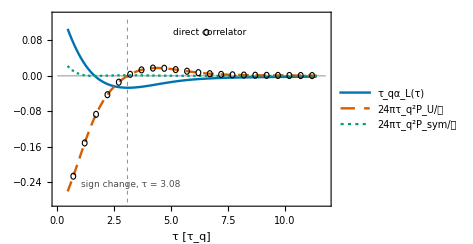

```mathematica
grn=RGBColor[0,0.62,0.45];Legended[Plot[{αI[s],RI[s],2 αI[s]^2},{s,0.45,11.4},PlotStyle->{Directive[blue,AbsoluteThickness[1.7]],Directive[verm,AbsoluteThickness[1.7],Dashing[{0.022,0.014}]],Directive[grn,AbsoluteThickness[1.6],Dashing[{0.005,0.007}]]},PlotRange->{{0,11.8},{-0.285,0.135}},Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[0.9]],FrameLabel->{lab[Row[{it["τ"],"   [",Subscript[it["τ"], "q"],"]"}]],None},FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->10],Prolog->{Directive[GrayLevel[0.5],AbsoluteThickness[0.6]],Line[{{0,0},{11.8,0}}],Directive[GrayLevel[0.55],AbsoluteThickness[0.7],Dashing[{0.008,0.008}]],Line[{{3.079,-0.285},{3.079,0.135}}]},Epilog->{Directive[Black,AbsoluteThickness[0.8]],(Circle[#,{0.105,0.0068}]&)/@pts,Text[Style[Row[{"sign change, ",it["τ"]," = 3.08"}],FontFamily->"Times",FontSize->9,GrayLevel[0.3]],{3.24,-0.245},{-1,0}],Circle[{6.55,0.098},{0.105,0.0068}],Text[Style["  direct correlator",FontFamily->"Times",FontSize->9,Black],{6.7,0.098},{-1,0}]},ImageSize->350,AspectRatio->0.7,ImagePadding->{{52,10},{42,8}}],Placed[LineLegend[{Directive[blue,AbsoluteThickness[1.7]],Directive[verm,AbsoluteThickness[1.7],Dashing[{0.022,0.014}]],Directive[grn,AbsoluteThickness[1.6],Dashing[{0.005,0.007}]]},{lab[Row[{Subscript[it["τ"], "q"],Subscript[it["α"], "L"],"(",it["τ"],")"}]],lab[Row[{"24π",Superscript[Subscript[it["τ"], "q"],"2"],Subscript[it["P"], "U"],"/𝒩"}]],lab[Row[{"24π",Superscript[Subscript[it["τ"], "q"],"2"],Subscript[it["P"], "sym"],"/𝒩"}]]},LegendMarkerSize->26,Spacings->0.3],{0.71,0.3}]]
```